# Homework 1

## PHYS 600 Sep 8, 2023

## Numerical Integration

```mathematica
f[Ω_, z_]:= 1/((Ω (1+z)^3+(1-Ω)(1+z)^(3/2))^(1/2));
```

```mathematica
integrateFunction[Ω_?NumericQ,z0_?NumericQ]:=NIntegrate[f[Ω,z],{z,0,z0}];
```

```mathematica
ΩValues={0,0.3,0.7,1};
```

```mathematica
(*Generate a plot for each Ω*)
plots=Table[
Plot[
integrateFunction[i,z0],{z0,0,1},
PlotStyle->ColorData[97,"ColorList"][[i]],
AxesLabel->{"z","Integration Result"},
Frame->True,
FrameLabel->{{"Integration Result",None},{"z",None}},
LabelStyle->{FontSize->14},
PlotRange->All,
PlotLegends->Placed[
{"Ω = "<>ToString[ΩValues[[i]]]},{0.7,0.1}
]
],{i,Length[ΩValues]}
];
```

## Analytic Integration

```mathematica
Ω=0:
(∫_0)^z 1/(1+z')^(3/4)ⅆz'=(∫_1)^(1+z)u^(-3/4)ⅆu=4(1+z)^(1/4)-4
```

```mathematica
Ω=1:
(∫_0)^z 1/(1+z')^(3/2)ⅆz'=(∫_1)^(1+z)u^(-3/2)ⅆu=2-2/(1+z)^(1/2)
```

## Plot

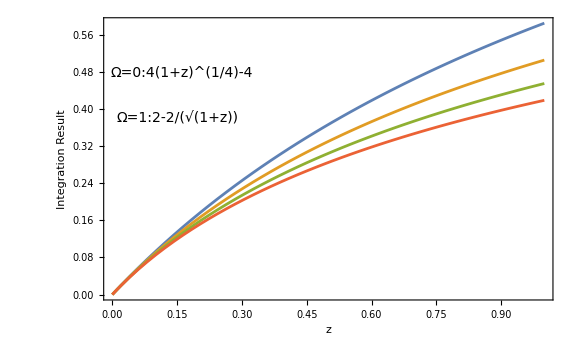

```mathematica
combinedPlot=Show[
plots,
PlotRange->All,
ImageSize->Large,
Epilog->{Text[Style["Ω=0:4(1+z)^(1/4)-4",14],{0.16,0.48}], Text[Style["Ω=1:2-2/(√(1+z))",14],{0.15,0.38}]}
]
```

```mathematica
(*Export image to png*)
Export["/Users/yaronetokayer/Yale Drive/Classes/PHYS 600/phys600 hw/phys600 hw 1/combined_plot.png",combinedPlot];
```

```mathematica
(*Export the notebook as a PDF*)
NotebookSave[];
NotebookPrint[InputNotebook[],"/Users/yaronetokayer/Yale Drive/Classes/PHYS 600/phys600 hw/phys600 hw 1/phys600 hw 1 printout.pdf"]
```